Веркович, 221703
Лабораторная работа №4
Численное решение нелинейных уравнений
Вариант 1

Задание № 1

а) Отделяем корни :

```mathematica
f[x_]:= 15*x^3-86*x^2+111*x-28(*функция*)
```

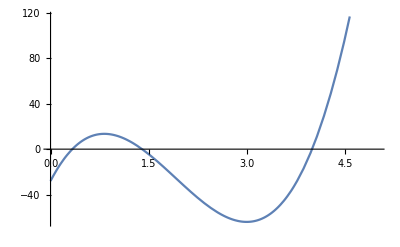

```mathematica
FunkGraphic=Plot[f[x],{x,0,5}]
```

Отделяем корни графически. Корнями уравнения будут точки, в которых
  график пересекает ось абсцисс. Таких точек 3: на отрезке [0,1], [1,2], [2,5]
  Найдем корень на отрезке [0,1]
  б) Находим приближенный корень уравнения :

```mathematica
a=0;
b=1;
epsilon=10^-3;
methodChord[f_]:=Module[{x1=a,x2=b,x3,k=1},
While[ Abs[x2-x1]>epsilon,
x3=x1-(f[x1]*(x2-x1))/(f[x2]-f[x1]);
x1=x2;
x2=x3;
k++;
];
{x2,k}
]; (*Функция для метода Хорд*)
{aproxRoot, itNum}=methodChord[f];
Print["Приближенный корень уравнения: ", N[aproxRoot,3],"; Количество итераций: ", itNum]
```

Приближенный корень уравнения: 0.333; Количество итераций: 10

3)Находим первые два приближения функции:

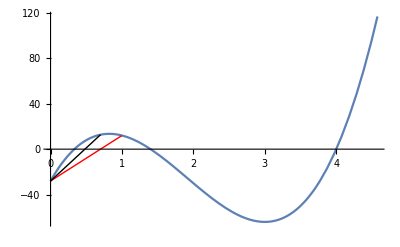

```mathematica
Chord1=Line[{{a,f[a]},{b,f[b]}}];(*Первая хорда*)
SecondAprox=b-(f[b]*(b-a))/(f[b]-f[a]);
Chord2=Line[{{a,f[a]},{SecondAprox,f[SecondAprox]}}];(*Вторая хорда*)
Show[FunkGraphic, Graphics[{Red,Chord1,Black,Chord2}],PlotRange->{{0,2.5},{100,-100}}]
```

Задание № 2

```mathematica
Clear[f];
f=x^6+6*x^5+12*x^4+6*x^3-9*x^2-12*x-4
```

-4-12 x-9 x^2+6 x^3+12 x^4+6 x^5+x^6

Решение с помощью Solve :

```mathematica
Solve[f==0,x]
```

{{x→-2},{x→-2},{x→-1},{x→-1},{x→-1},{x→1}}

Решение с помощью NSolve :

```mathematica
NSolve[f==0,x]
```

{{x→-2.},{x→-2.},{x→-1.},{x→-1.},{x→-1.},{x→1.}}

Решение с помощью  Roots :

```mathematica
Roots[f==0,x]
```

x==-2||x==-2||x==-1||x==-1||x==-1||x==1

Решение с помощью  FindRoot :

```mathematica
FindRoot[f==0,{x,1}]
```

{x→1.}

Разложение на множители с помощью Factor :

```mathematica
Factor[f]
```

(-1+x) (1+x)^3 (2+x)^2

Графически отделим корни :

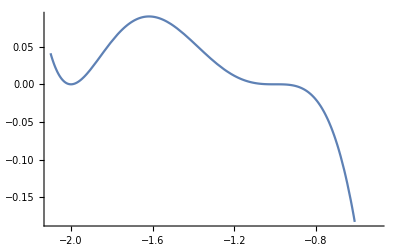

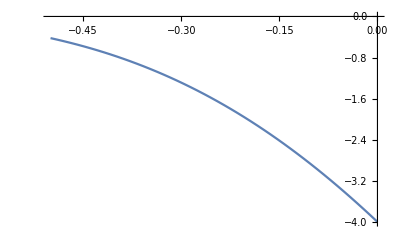

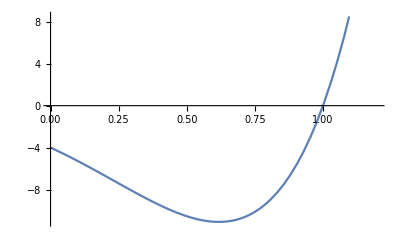

```mathematica
Plot[f,{x,-2.1, -0.5}]
Plot[f,{x,-0.5,0}]
Plot[f,{x,0,1.2}](*Графика 3, тк на отрезках [-2.1,-0.5] и[-0.5, 0] изгибы графика фукнции очень малы и не видны
в определённом масштабе, например на отрезке от [-3,3] *)
```

Задание № 3

```mathematica
Clear[f]
f[x_]:=3^x-4*x-2
```

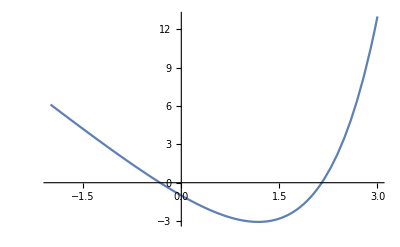

```mathematica
(*Отделяем корни*)
Plot[f[x],{x,-2,3}]
```

a) Метод Ньютона :

```mathematica
methodNewton[f_]:=Module[{xk0=1,xk1=0,n=1},
While[ Abs[xk0-xk1]>epsilon,
xk1=xk0-f[xk0]/f'[xk0];
xk0=xk1;
n++;
];
{xk1,n}
];(*Функция для метода Ньютона*)
{aproxRootN, itNumN}=methodNewton[f];
Print["Приближенный корень уравнения: ", N[aproxRootN,3],"; Количество итераций: ", itNumN]
```

Приближенный корень уравнения: -3.26; Количество итераций: 2

б) Метод секущих

```mathematica
methodSec[g_]:=Module[{xk0=1,xk1=2,xk2,n=1,epsilon=1/1000},
While[Abs[xk1-xk0]>epsilon,
xk2=xk1-(g[xk1]*(xk1-xk0))/(g[xk1]-g[xk0]);
xk0=xk1;
xk1=xk2;
n++;];
{xk1,n}
];(*Функция для метода секущих*)
{aproxRootS, itNumS}=methodSec[f];
Print["Приближенный корень уравнения: ", N[aproxRootS,3],"; Количество итераций: ", itNumS]
```

Приближенный корень уравнения: 2.15; Количество итераций: 6

Задание № 4

```mathematica
fi[x_]:=(3^x/x)-4-(2/x)
```

```mathematica
methodSimpleIt[g_]:=Module[{xk1=1,xk2=0,k=1},
While[Abs[xk2-xk1]>epsilon,
xk2=g[xk1];
xk1=xk2;
k++;];
{xk2,k}
];(*Функция для метода секущих*)
{aproxRootSit, itNumSit}=methodSimpleIt[fi];
Print["Приближенный корень уравнения: ", N[aproxRootSit,3],"; Количество итераций: ", itNumSit]
```

Приближенный корень уравнения: -3.; Количество итераций: 2

Задание № 5

```mathematica
Clear[f]
f=3^x-4*x-2
```

-2+3^x-4 x

```mathematica
N[Solve[f==0,x]]
N[NSolve[f==0,x]]
N[FindRoot[f,{x,0}]]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.325081},{x→2.14839}}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{x→-0.325081},{x→2.14839}}

{x→-0.325081}

Задание №6

```mathematica
Clear[f]
```

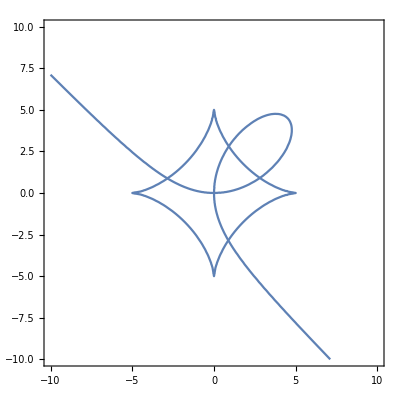

```mathematica
f[x_,y_]:=(x^2)^(1/3)+(y^2)^(1/3)-25^(1/3);
g[x_,y_]:=x^3+y^3-9*x*y;

gr1=ContourPlot[f[x,y]==0,{x,-10,10},{y,-10,10}];
gr2=ContourPlot[g[x,y]==0,{x,-10,10},{y,-10,10}];
Show[gr1,gr2]
```

```mathematica
FindRoot[{f[x,y],g[x,y]},{x,-5},{y,1}]
FindRoot[{f[x,y],g[x,y]},{x,0},{y,2}]
FindRoot[{f[x,y],g[x,y]},{x,4},{y,1}]
FindRoot[{f[x,y],g[x,y]},{x,1},{y,-3}]
```

{x→-2.8479,y→0.875031}

{x→0.903822,y→2.80557}

{x→2.80557,y→0.903822}

{x→0.875031,y→-2.8479}